## Applications of stochastic processes

## Markov processes; Transition matrix

#### Reproduction in discrete time

i) I will explore here a discrete-time exponential growth model and discrete-time logistic growth model.
In the discrete-time exponential growth model each reproducing individual is replaced by a constant number of individuals in the next discrete-time unit. In this model, births and deaths are affecting the numbers of individuals in the population n(t). Here, b gives the number of births, d gives the fraction of the population that dies in each interval. 

Discrete-time exponential growth model
A deterministic model of an exponential population growth in discrete time is n(t + 1) = (1- d) (1 +b) n(t) = R n(t), where (1- d) is the fraction of individuals that survive, and R is the number of individuals that survive in each time unit. 
In a stochastic model we draw a random number representing the total number of offspring at n(t). We could also draw a random set of numbers; then, their sum gives the total number of offspring at n(t).
Usually, the number of surviving offspring per reproducing individual follow a Poisson distribution. Here, R represents the mean number of offspring per reproducing individual, which is drawn from the randomly from a Poisson distribution, where the mean is given by μ=R n(t). Then, I also introduce fitness w where w(n) =r exp(-θn). Here fitness is dependent on the number of individuals in a population. In other words as population size increases as individuals compete for resources resulting in a plateauing population size after a certain number of generations.

Discrete-time logistic growth model
In a logistic growth model factors such a density dependent competition for resources slow down the growth of a population
These processes are incorporated in a discrete-time logistic growth model which assumes that R declines as the population grows.  In a deterministic model n(t + 1) = n(t) + r n(t) (1 - (n(t))/K), where r gives a growth rate, measuring whether population grows or shrinks, and K is a carrying capacity or the population size at which each individual replaces itself therefore sustaining it self at this maximum population size. In a stochastic model the mean of the Poisson distribution will be density dependent of the population size in a given time unit R(n) = 1 + r(1- n(t)/K. 

It is interesting to compare discrete-time exponential growth model with introduced fitness constraints to the discrete-time logistic growth model. In the latter the growth constraint is modelled more explicitly by setting  the carrying capacity K to a certain value (500 N in my simulation below).

ii) and iii)

Discrete-time exponential growth model
Here, μ=1.2, initial population size is set to n(0)=5. The plot shows five replicates of the simulation over 100 generations. I then replicate the simulation 100 times with the same initial values and the parameter set and save it in a table format.

```mathematica
egr = Table[NestWhileList[expgrowth[1.2],5,Positive,1,100],{1000}];
Sort[egr⟦All,-1⟧];
```

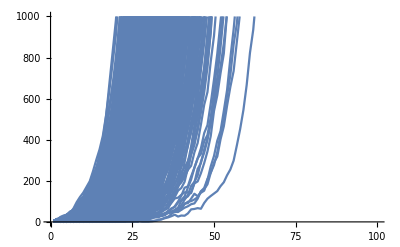

```mathematica
Show[Table[ListLinePlot[egr⟦i⟧,PlotRange->{{0,100},{0,1000}}],{i,1000}]]
```

The mean number of surviving individuals after 100 generations is:

```mathematica
Mean[egr⟦All,-1⟧]//N
```

4.23041×10^8

The fraction of extinct individuals is 0.16:

```mathematica
Count[egr⟦All,-1⟧,0]/1000 // N
```

0.139

Now, I introduce fitness constraints in the model by specifying the growth rate r and theta when randomly sampling from the mean of a Poisson distribution. Population size plateaus at around 150 individuals. Distribution of times to extinction is bimodal, the population either dies out quickly (with a mean of 8.8 generations) or survives until the end of the simulation (100 generations here).

```mathematica
epxrlim = Table[NestWhileList[expExctinct2[1.2, 0.001],5,Positive,1,100],{1000}];
Sort[epxrlim⟦All,-1⟧];
```

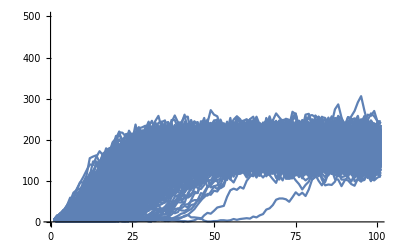

```mathematica
Show[Table[ListLinePlot[epxrlim⟦i⟧,PlotRange->{{0,100},{0,500}}],{i,1000}]]
```

The mean number of surviving individuals after 100 generations is:

```mathematica
Mean[epxrlim⟦All,-1⟧]//N
```

155.601

The fraction of extinct individuals is:

```mathematica
Count[epxrlim⟦All,-1⟧,0]/1000 // N
```

0.134

Distribution of times to extinction and the expected time to extinction:

```mathematica
Sort[Length/@ epxrlim];
```

```mathematica
extict = Pick[Length/@ epxrlim, # < 101&/@Length/@ epxrlim];
```

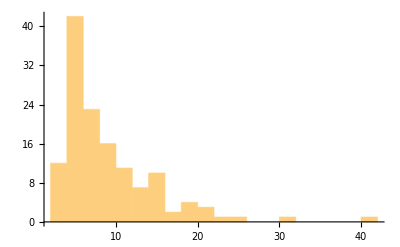

{8.56716}

```mathematica
Histogram[extict]
{Mean[extict]} // N
```

Now, it is interesting to also look at the simulations using a discrete-time logistic growth model, where the upper limits to growth are modeled more explicitly, by setting carrying capacity K to a certain population size. I set the growth rate at r=1.2, the maximum population size at which the population can sustain itself K=150 and the initial population size is set to n(0)=5. The plot shows 100 replicates of the simulation over 100 generations. I then replicate the simulation 1000 times with the same initial values and the parameter set and save it in a table format showing the distribution of the surviving offspring. For simplicity here, the function logrowth below is only sampling the total population number at each time step (see in the function description below). Populations reach the carrying capacity within few generations, much quicker that in the exponential growth rate model with fitness constraints, but the mean number of surviving individuals is lower than in the exponential growth rate model with fitness constraints.

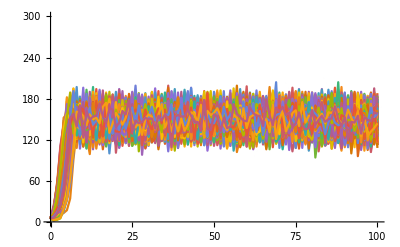

```mathematica
plotlog=List[];
For[i=1,i<1001,i++,(a=ListLinePlot[Table[{t,logrowth[t,1.2,150,5,i]},{t,0,100}],PlotStyle->ColorData[97,i+1], 
PlotRange->{{0,100},{0,300}}];
AppendTo[plotlog,a])];
Show[plotlog]
```

```mathematica
simullog=Sort[Table[logrowth[100,0.1,100, 5,rep],{rep,1,100}]];
```

The mean number of surviving individuals after 1000 generations is:

```mathematica
Mean[simullog]//N
```

52.59

The fraction of extinct individuals is:

```mathematica
Count[simullog,0]/100 // N
```

0.43

iv) 
I populate transition matrix M_(i,j)=Poisson(w*i)=((ⅇ^-iw(iw))^j)/(j!) supposing that the fitness, w, decreases with larger population size w(n)=r exp(-θn). Here, n gives the number of states, and as before, r gives the growth rate r=1.2, and theta is set to θ=0.001. Predictions of the expected time to extinction correspond to the one obtained from the simulations.

```mathematica
n=100;
r=1.2;
theta = 0.001;
P = Table[N[If[j == 0 && i ==  0, 1, Exp[-i r Exp[- theta i]]*(i r Exp[- theta i])^(j)/Factorial[j]]], {i,0, n},{j,0, n}];P//MatrixForm;
```

```mathematica
{Eigenvalues[P],Eigenvectors[Transpose[P],-1]};
```

```mathematica
P0=Transpose[Drop[Transpose[Drop[P,1]],1]];
Inverse[IdentityMatrix[100]-P0].ConstantArray[1,100];
```

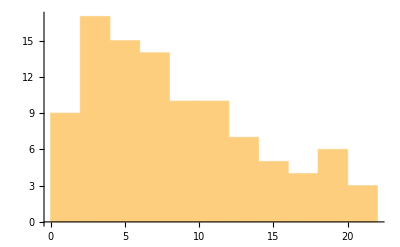

{8.44323}

```mathematica
Histogram[Inverse[IdentityMatrix[100]-P0].ConstantArray[1,100], 10]
{Mean[Inverse[IdentityMatrix[100]-P0].ConstantArray[1,100]]} // N
```

#### Function definitions

```mathematica
logrowth::usage="logrowth[t, r, k, n0, rep] gives a logistic population growth over time. 
t gives the number of discrete-time units or generations; r gives the
growth rate; n0 gives the initial population size at n(0); k gives the maximum population size at which 
the population can sustain itself; rep replicates the simulation with the same initial conditions and parameters";
logrowth[t_,r_,k_,n0_,rep_]:=logrowth[t,r,k,n0,rep]=If[logrowth[t-1,r,k,n0,rep]>0,
    Random[PoissonDistribution[
	logrowth[t-1,r,k,n0,rep]+r*logrowth[t-1,r,k,n0,rep]*
	(1-logrowth[t-1,r,k,n0,rep]/k)]],0]
logrowth[0,r_,k_,n0_,rep_]:=n0
```

```mathematica
expgrowth::usage="expExctinct[mu][i] gives an exponential population growth over a 
specified number of generations. mu gives the
mean of a Poisson distribution; i gives the number of offsring randomly chosen from a Poisson ditribution.";
expgrowth[mu_][i_]:=Module[{}, expgrowth[mu, i]=If[i>0,
    RandomInteger[PoissonDistribution[mu i]], 0]];
```

```mathematica
expExctinct2::usage="expExctinct2[r, theta][i] gives an exponential population growth where fitness decreases
with population size; r give the growth rate, theta gives dependence of the fitness with i, where 
i gives the number of offsring randomly chosen from a Poisson ditribution.";
expExctinct2[r_, theta_][i_]:=Module[{}, expExctinct2[r, theta, i]=If[i>0,
    RandomInteger[PoissonDistribution[i r Exp[-thetai]]], 0]];
```